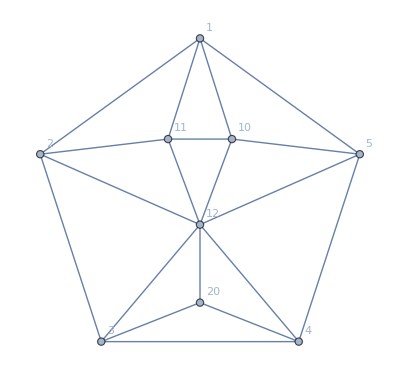

```mathematica
contractedOnce=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,10<->11,11<->12,12<->10,1<->10,1<->11,2<->11,2<->12,12<->20,5<->10,5<->12,3<->12,3<->20,4<->12,4<->20}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

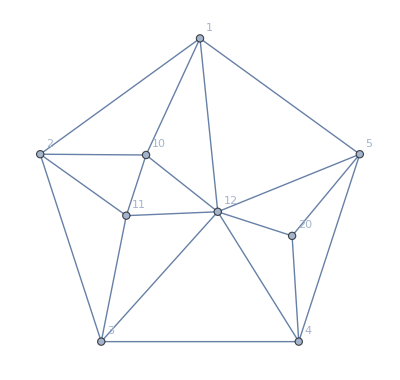

```mathematica
contractedOnce2=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,10<->11,11<->12,12<->10,2<->10,2<->11,3<->11,3<->12,12<->20,1<->10,1<->12,4<->12,4<->20,5<->12,5<->20}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

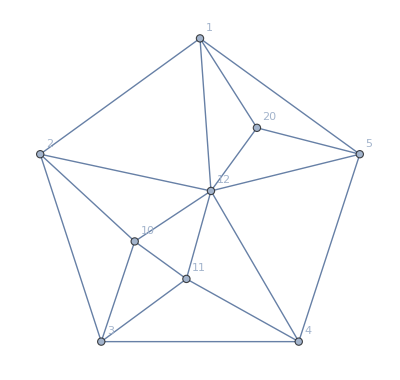

```mathematica
contractedOnce3=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,10<->11,11<->12,12<->10,
3<->10,3<->11,4<->11,4<->12,12<->20,2<->10,2<->12,5<->12,5<->20,1<->12,1<->20}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

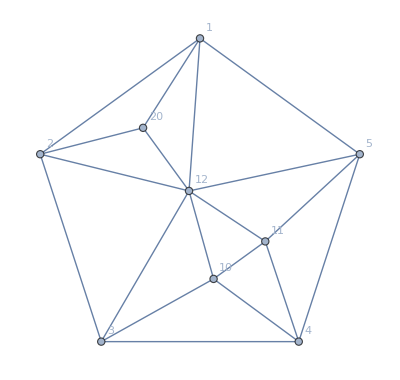

```mathematica
contractedOnce4=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,10<->11,11<->12,12<->10,
4<->10,4<->11,5<->11,5<->12,12<->20,3<->10,3<->12,1<->12,1<->20,2<->12,2<->20}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

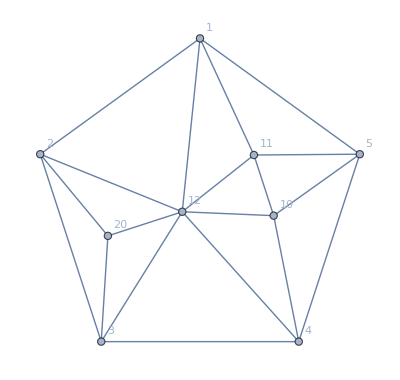

```mathematica
contractedOnce5=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,10<->11,11<->12,12<->10,
5<->10,5<->11,1<->11,1<->12,12<->20,4<->10,4<->12,2<->12,2<->20,3<->12,3<->20}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

```mathematica
GraphSolutions3[contractedOnce,x1==1&&x2==2&&x3==1&&x4==2&&x5==3]
```

{{x1→1,x2→2,x3→1,x4→2,x5→3,x10→2,x11→3,x12→4,x20→3}}

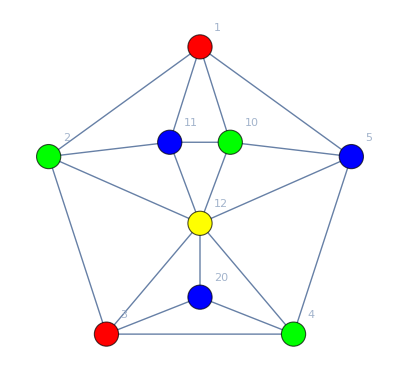

```mathematica
Table[
PaintGraph2[g,"x1==1&&x2==2&&x3==1&&x4==2&&x5==3",VertexSize->Large, GraphLayout->"TutteEmbedding"],
{g,{contractedOnce,contractedOnce2,contractedOnce2,contractedOnce2,contractedOnce2}}
]
```

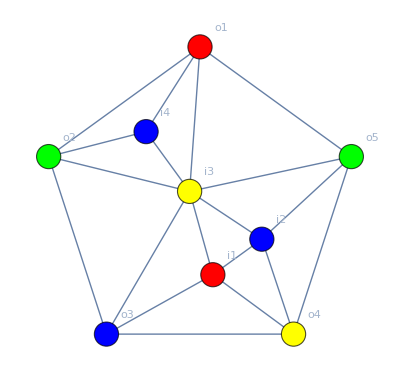
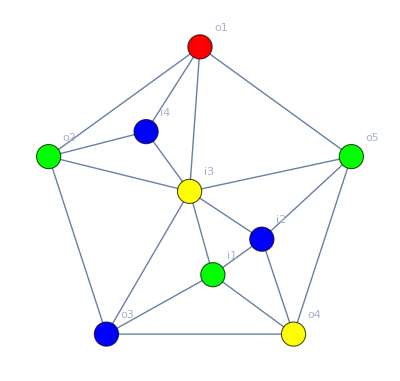

```mathematica
Table[
PaintGraph2[g,"x1==1&&x2==2&&x3==3&&x4==4&&x5==2&&((x11==x20)||(x12==x20))",VertexLabels->{1->"o1",2->"o2",3->"o3",4->"o4",5->"o5",10->"i1",11->"i2",12->"i3",20->"i4"},VertexSize->Large, GraphLayout->"TutteEmbedding"],
{g,{contractedOnce,contractedOnce2,contractedOnce3,contractedOnce4,contractedOnce5}}
]
```

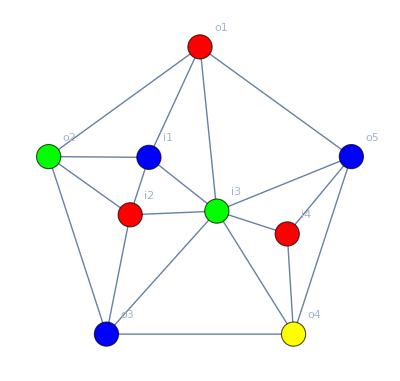
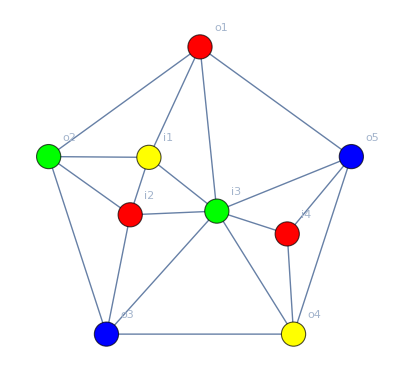

```mathematica
Table[
PaintGraph2[g,"x1==1&&x2==2&&x3==3&&x4==4&&x5==3&&((x11==x20)||(x12==x20))",VertexLabels->{1->"o1",2->"o2",3->"o3",4->"o4",5->"o5",10->"i1",11->"i2",12->"i3",20->"i4"},VertexSize->Large, GraphLayout->"TutteEmbedding"],
{g,{contractedOnce,contractedOnce2,contractedOnce3,contractedOnce4,contractedOnce5}}
]
```

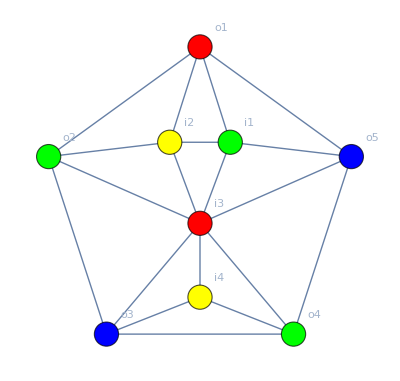
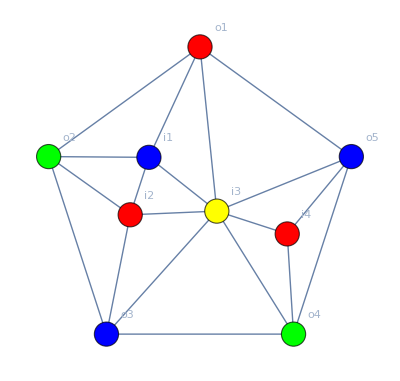

```mathematica
Table[
PaintGraph2[g,"x1==1&&x2==2&&x3==3&&x4==2&&x5==3&&((x11==x20)||(x12==x20))",VertexLabels->{1->"o1",2->"o2",3->"o3",4->"o4",5->"o5",10->"i1",11->"i2",12->"i3",20->"i4"},VertexSize->Large, GraphLayout->"TutteEmbedding"],
{g,{contractedOnce,contractedOnce2,contractedOnce3,contractedOnce4,contractedOnce5}}
]
```

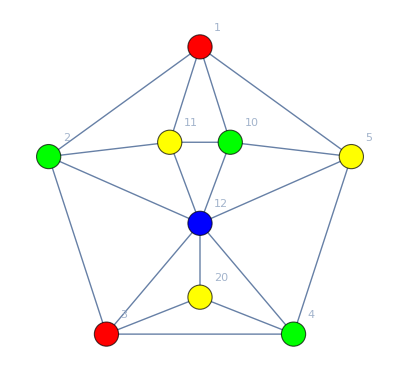
{-Graphics-,-Graphics-}

```mathematica
PaintGraph2[contractedOnce,"x1==1&&x2==2&&x3==1",VertexSize->Large, GraphLayout->"TutteEmbedding"]
```

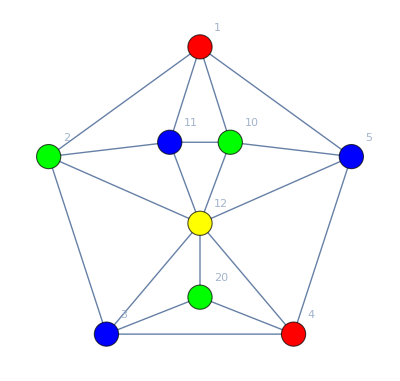
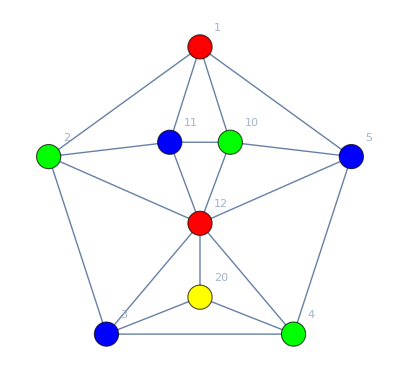
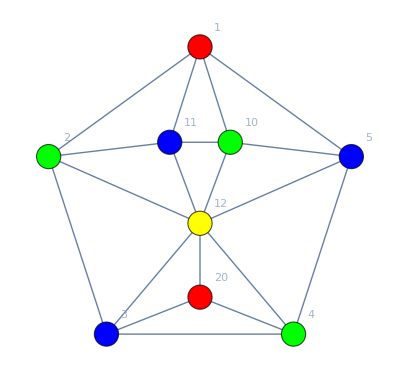
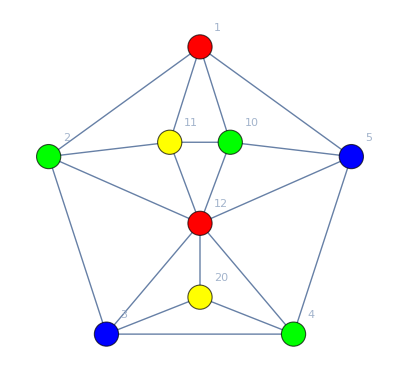
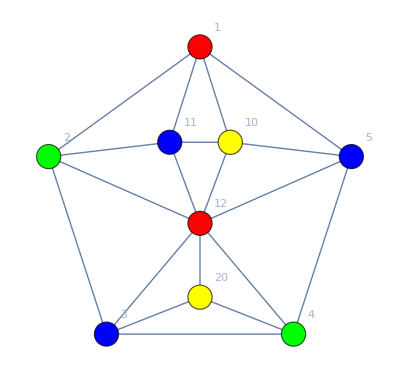
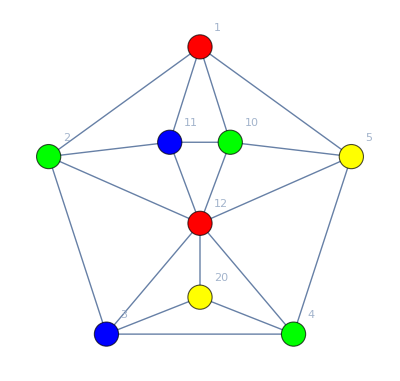
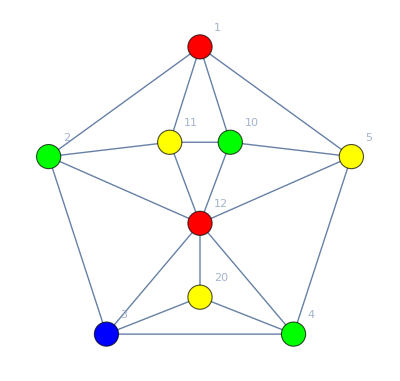
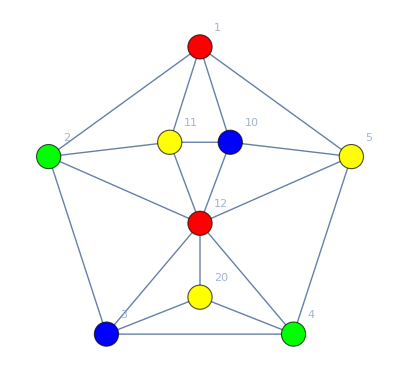

```mathematica
PaintGraph2[contractedOnce,"x1==1&&x2==2&&x3==3",VertexSize->Large, GraphLayout->"TutteEmbedding"]
```

```mathematica
GraphSolutions3[g_,pre_]:=Block[{sols, cond},
cond=ToLogical[g]&&pre;
(*cond=Symbol["x"<>ToString[cycle[[1]]]] ==1 && Symbol["x"<>ToString[cycle[[2]]]] ==2 && cond;*)
sols=Solve[cond,SymbolRange[g]];
Map[Sort[#,SymbolComp[#1[[1]],#2[[1]]]&]&,sols]
]
```

```mathematica
allsols=Block[{res=Association[], resValue=Association[],result={}},
Table[
With[
{key={x1,x2,x3,x4,x5}/.sol,
value={x10,x11,x12,x20}/.sol},
With[{valueGood=value[[1]]==value[[4]]||value[[2]]==value[[4]]},
With[{value2={valueGood,value}},
If[KeyExistsQ[res,key],
res[key]=Join[res[key],{value2}];
resValue[key]=resValue[key]||valueGood;
,
res[key]={value2};
resValue[key]=valueGood
]
]
]
],
{sol,Join[GraphSolutions3[contractedOnce,x1==1&&x2==2&&x3==3],GraphSolutions3[contractedOnce,x1==1&&x2==2&&x3==1]]}
];
Table[
If[!resValue[key],AppendTo[result,{key->res[key]}]]
,{key,Keys[res]}
];
Sort[result]]//TableForm
```

{1,2,3,4,2}→{{False,{3,4,1,2}},{False,{4,3,1,2}}}

```mathematica
TableForm[allsols]
```

{1,2,3,4,2}→{{False,{3,4,1,2}},{False,{4,3,1,2}}}
{1,2,4,3,2}→{{False,{3,4,1,2}},{False,{4,3,1,2}}}

```mathematica
exp=ToLogical[contractedOnce]
```

x1∈Integers&&x2∈Integers&&x3∈Integers&&x4∈Integers&&x5∈Integers&&x10∈Integers&&x11∈Integers&&x12∈Integers&&x20∈Integers&&1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x4≤4&&1≤x5≤4&&1≤x10≤4&&1≤x11≤4&&1≤x12≤4&&1≤x20≤4&&x1≠x2&&x2≠x3&&x3≠x4&&x4≠x5&&x5≠x1&&x10≠x11&&x11≠x12&&x12≠x10&&x1≠x10&&x1≠x11&&x2≠x11&&x2≠x12&&x12≠x20&&x5≠x10&&x5≠x12&&x3≠x12&&x3≠x20&&x4≠x12&&x4≠x20

```mathematica
Block[{x3b,x4b,x5b,result={}, sol},
For[x3b=1,x3b<4,x3b++,
If[x3b≠2,
For[x4b=1,x4b<4,x4b++,
If[x4b≠x3b,
For[x5b=2,x5b<4,x5b++,
If[x5b≠x4b,
sol=Solve[exp&&x1==1&&x2==2&&x3==x3b&&x4==x4b&&x5==x5b && (x20==x11||x20==x12),{x10,x11,x12,x20}];
If[sol=={},
Print[{x3b,x4b,x5b}]
];
AppendTo[result,sol]
]
]
]
]
]
];
result
]
```

{1,3,2}

{3,1,2}

{3,1,3}

{{{x10→ConditionalExpression[2,x1==1&&x2==2&&x3==1&&x4==2&&x5==3],x11→ConditionalExpression[3,x1==1&&x2==2&&x3==1&&x4==2&&x5==3],x12→ConditionalExpression[4,x1==1&&x2==2&&x3==1&&x4==2&&x5==3],x20→ConditionalExpression[3,x1==1&&x2==2&&x3==1&&x4==2&&x5==3]}},{},{},{},{{x10→ConditionalExpression[2,x1==1&&x2==2&&x3==3&&x4==2&&x5==3],x11→ConditionalExpression[4,x1==1&&x2==2&&x3==3&&x4==2&&x5==3],x12→ConditionalExpression[1,x1==1&&x2==2&&x3==3&&x4==2&&x5==3],x20→ConditionalExpression[4,x1==1&&x2==2&&x3==3&&x4==2&&x5==3]}}}

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,10<->11,11<->12,12<->10,1<->10,1<->11,2<->11,2<->12,12<->20,5<->10,5<->12,3<->12,3<->20,4<->12,4<->20}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

-Graphics-

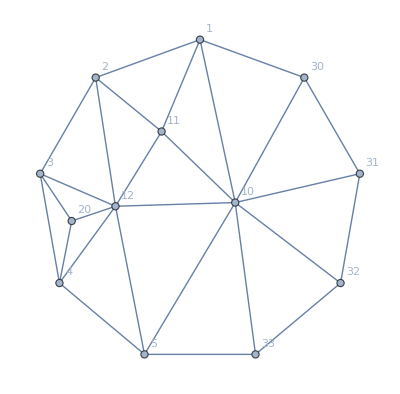

```mathematica
contractedOnceB=Graph[{1<->2,2<->3,3<->4,4<->5,10<->11,11<->12,12<->10,1<->10,1<->11,2<->11,2<->12,12<->20,5<->10,5<->12,3<->12,3<->20,4<->12,4<->20,1<->30,30<->31,31<->32,32<->33,33<->5,10<->30,10<->31,10<->32,10<->33}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

```mathematica
allsols2=Block[{res=Association[], resValue=Association[],result={}},
Table[
With[
{key={x1,x2,x3,x4,x5}/.sol,
value={x10,x11,x12,x20,x30,x31,x32,x33}/.sol},
With[{valueGood=value[[1]]==value[[4]]||value[[2]]==value[[4]]},
With[{value2={valueGood,value}},
If[KeyExistsQ[res,key],
res[key]=Join[res[key],{value2}];
resValue[key]=resValue[key]||valueGood;
,
res[key]={value2};
resValue[key]=valueGood
]
]
]
],
{sol,GraphSolutions3[contractedOnceB,x1==1&&x2==2]}
];
Table[
If[!resValue[key],AppendTo[result,{key->res[key]}]]
,{key,Keys[res]}
];
Sort[result]]//TableForm
```

{1,2,3,2,1}→{{False,{2,3,4,1,3,1,3,4}},{False,{2,3,4,1,3,1,4,3}},{False,{2,3,4,1,3,4,1,3}},{False,{2,3,4,1,3,4,1,4}},{False,{2,3,4,1,3,4,3,4}},{False,{2,3,4,1,4,1,3,4}},{False,{2,3,4,1,4,1,4,3}},{False,{2,3,4,1,4,3,1,3}},{False,{2,3,4,1,4,3,1,4}},{False,{2,3,4,1,4,3,4,3}}}
{1,2,3,4,2}→{{False,{3,4,1,2,2,1,2,1}},{False,{3,4,1,2,2,1,2,4}},{False,{3,4,1,2,2,1,4,1}},{False,{3,4,1,2,2,4,1,4}},{False,{3,4,1,2,2,4,2,1}},{False,{3,4,1,2,2,4,2,4}},{False,{3,4,1,2,4,1,2,1}},{False,{3,4,1,2,4,1,2,4}},{False,{3,4,1,2,4,1,4,1}},{False,{3,4,1,2,4,2,1,4}},{False,{3,4,1,2,4,2,4,1}},{False,{4,3,1,2,2,1,2,1}},{False,{4,3,1,2,2,1,2,3}},{False,{4,3,1,2,2,1,3,1}},{False,{4,3,1,2,2,3,1,3}},{False,{4,3,1,2,2,3,2,1}},{False,{4,3,1,2,2,3,2,3}},{False,{4,3,1,2,3,1,2,1}},{False,{4,3,1,2,3,1,2,3}},{False,{4,3,1,2,3,1,3,1}},{False,{4,3,1,2,3,2,1,3}},{False,{4,3,1,2,3,2,3,1}}}
{1,2,4,2,1}→{{False,{2,4,3,1,3,1,3,4}},{False,{2,4,3,1,3,1,4,3}},{False,{2,4,3,1,3,4,1,3}},{False,{2,4,3,1,3,4,1,4}},{False,{2,4,3,1,3,4,3,4}},{False,{2,4,3,1,4,1,3,4}},{False,{2,4,3,1,4,1,4,3}},{False,{2,4,3,1,4,3,1,3}},{False,{2,4,3,1,4,3,1,4}},{False,{2,4,3,1,4,3,4,3}}}
{1,2,4,3,2}→{{False,{3,4,1,2,2,1,2,1}},{False,{3,4,1,2,2,1,2,4}},{False,{3,4,1,2,2,1,4,1}},{False,{3,4,1,2,2,4,1,4}},{False,{3,4,1,2,2,4,2,1}},{False,{3,4,1,2,2,4,2,4}},{False,{3,4,1,2,4,1,2,1}},{False,{3,4,1,2,4,1,2,4}},{False,{3,4,1,2,4,1,4,1}},{False,{3,4,1,2,4,2,1,4}},{False,{3,4,1,2,4,2,4,1}},{False,{4,3,1,2,2,1,2,1}},{False,{4,3,1,2,2,1,2,3}},{False,{4,3,1,2,2,1,3,1}},{False,{4,3,1,2,2,3,1,3}},{False,{4,3,1,2,2,3,2,1}},{False,{4,3,1,2,2,3,2,3}},{False,{4,3,1,2,3,1,2,1}},{False,{4,3,1,2,3,1,2,3}},{False,{4,3,1,2,3,1,3,1}},{False,{4,3,1,2,3,2,1,3}},{False,{4,3,1,2,3,2,3,1}}}

```mathematica
TableForm[allsols2]
```

{1,2,3,4,2}→{{False,{3,4,1,2}},{False,{4,3,1,2}}}
{1,2,4,3,2}→{{False,{3,4,1,2}},{False,{4,3,1,2}}}

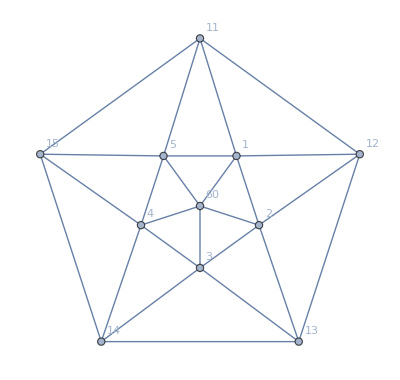

```mathematica
notContracted2=Graph[{
1<->2,2<->3,3<->4,4<->5,5<->1,
11<->12,12<->13,13<->14,14<->15,15<->11,
1<->11,1<->12,2<->12,2<->13,3<->13,3<->14,4<->14,4<->15,5<->15,5<->11,
1<->60,2<->60,3<->60,4<->60,5<->60}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

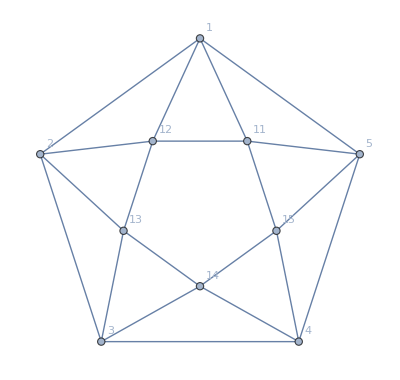

```mathematica
notContracted=Graph[{
1<->2,2<->3,3<->4,4<->5,5<->1,
11<->12,12<->13,13<->14,14<->15,15<->11,
1<->11,1<->12,2<->12,2<->13,3<->13,3<->14,4<->14,4<->15,5<->15,5<->11}, VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

```mathematica
Block[{res=Association[], resValue=Association[],result={}, sols},
Table[
With[
{key={x1,x2,x3,x4,x5}/.sol,
value={x11,x12,x13,x14}/.sol},
With[{valueGood=value[[1]]==value[[4]]||value[[2]]==value[[4]]},
With[{value2={valueGood,value}},
If[!valueGood,
Print["--------------------------------------"];
Print[key];
sols=GraphSolutions3[VertexContract[ notContracted,{12,15}],x1==key[[1]]&&x2==key[[2]]&&x3==key[[3]]&&x4==key[[4]]&&x5==key[[5]]];
Print[{{12,15},sols}];
If[sols=={},
sols=GraphSolutions3[VertexContract[ notContracted,{11,13}],x1==key[[1]]&&x2==key[[2]]&&x3==key[[3]]&&x4==key[[4]]&&x5==key[[5]]];
Print[{{11,13},sols}];
If[sols=={},
sols=GraphSolutions3[VertexContract[ notContracted,{12,14}],x1==key[[1]]&&x2==key[[2]]&&x3==key[[3]]&&x4==key[[4]]&&x5==key[[5]]];
Print[{{12,14},sols}];
If[sols=={},
Print["DAMN"]
]
]
]
]
]
]
],
{sol,GraphSolutions3[VertexContract[ notContracted,{13,15}],x1==1&&x2==2]}
]
]
```

--------------------------------------

{1,2,3,2,3}

{{12,15},{}}

{{11,13},{}}

{{12,14},{{x1→1,x2→2,x3→3,x4→2,x5→3,x11→2,x12→4,x13→1,x15→1}}}

--------------------------------------

{1,2,3,2,3}

{{12,15},{}}

{{11,13},{}}

{{12,14},{{x1→1,x2→2,x3→3,x4→2,x5→3,x11→2,x12→4,x13→1,x15→1}}}

--------------------------------------

{1,2,3,2,4}

{{12,15},{{x1→1,x2→2,x3→3,x4→2,x5→4,x11→2,x12→3,x13→1,x14→4},{x1→1,x2→2,x3→3,x4→2,x5→4,x11→2,x12→3,x13→4,x14→1}}}

--------------------------------------

{1,2,3,4,2}

{{12,15},{{x1→1,x2→2,x3→3,x4→4,x5→2,x11→4,x12→3,x13→1,x14→2},{x1→1,x2→2,x3→3,x4→4,x5→2,x11→4,x12→3,x13→4,x14→1},{x1→1,x2→2,x3→3,x4→4,x5→2,x11→4,x12→3,x13→4,x14→2}}}

--------------------------------------

{1,2,3,4,2}

{{12,15},{{x1→1,x2→2,x3→3,x4→4,x5→2,x11→4,x12→3,x13→1,x14→2},{x1→1,x2→2,x3→3,x4→4,x5→2,x11→4,x12→3,x13→4,x14→1},{x1→1,x2→2,x3→3,x4→4,x5→2,x11→4,x12→3,x13→4,x14→2}}}

--------------------------------------

{1,2,3,4,3}

{{12,15},{}}

{{11,13},{{x1→1,x2→2,x3→3,x4→4,x5→3,x11→4,x12→3,x14→1,x15→2},{x1→1,x2→2,x3→3,x4→4,x5→3,x11→4,x12→3,x14→2,x15→1}}}

--------------------------------------

{1,2,4,2,3}

{{12,15},{{x1→1,x2→2,x3→4,x4→2,x5→3,x11→2,x12→4,x13→1,x14→3},{x1→1,x2→2,x3→4,x4→2,x5→3,x11→2,x12→4,x13→3,x14→1}}}

--------------------------------------

{1,2,4,2,4}

{{12,15},{}}

{{11,13},{}}

{{12,14},{{x1→1,x2→2,x3→4,x4→2,x5→4,x11→2,x12→3,x13→1,x15→1}}}

--------------------------------------

{1,2,4,2,4}

{{12,15},{}}

{{11,13},{}}

{{12,14},{{x1→1,x2→2,x3→4,x4→2,x5→4,x11→2,x12→3,x13→1,x15→1}}}

--------------------------------------

{1,2,4,3,2}

{{12,15},{{x1→1,x2→2,x3→4,x4→3,x5→2,x11→3,x12→4,x13→1,x14→2},{x1→1,x2→2,x3→4,x4→3,x5→2,x11→3,x12→4,x13→3,x14→1},{x1→1,x2→2,x3→4,x4→3,x5→2,x11→3,x12→4,x13→3,x14→2}}}

--------------------------------------

{1,2,4,3,2}

{{12,15},{{x1→1,x2→2,x3→4,x4→3,x5→2,x11→3,x12→4,x13→1,x14→2},{x1→1,x2→2,x3→4,x4→3,x5→2,x11→3,x12→4,x13→3,x14→1},{x1→1,x2→2,x3→4,x4→3,x5→2,x11→3,x12→4,x13→3,x14→2}}}

--------------------------------------

{1,2,4,3,4}

{{12,15},{}}

{{11,13},{{x1→1,x2→2,x3→4,x4→3,x5→4,x11→3,x12→4,x14→1,x15→2},{x1→1,x2→2,x3→4,x4→3,x5→4,x11→3,x12→4,x14→2,x15→1}}}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
VertexList[VertexContract[ notContracted,{13,15}]]
```

{1,2,3,4,5,11,12,14,13}

```mathematica
ChromaticPolynomial[notContracted,4]
```

480

```mathematica
Permutations[{1,2,3,4,5}]//Length
```

120